# Tiling Scheme

## Construction of the asymmetric motif

I am creating my motif in a asymmetric way so that there is no reflective nor rotative symmetric.
Also, I tried to embed Golden Ratio in the formation of the motif. The yellow triangle is a golden triangle where the height and width has the ratio of (1 + sqrt(5)) : 2. Meanwhile, when placing the circle, the angle between the line connecting the center of the circle and the origin and the bottom line has a golden ratio with 90 degrees.

{{RGBColor[1, Rational[77, 255], Rational[148, 255]],Polygon[…]},{RGBColor[1, 1, 0],Triangle[{{0,0},{0,2/(1+√5)},{1,0}}]},{RGBColor[0, 0, 1],Thickness[0.01],Circle[{0,0},1,{0,π/2}]},{RGBColor[Rational[2, 5], Rational[194, 255], 1],Opacity[0.5],Disk[{0.395244,0.577739},0.3]}}

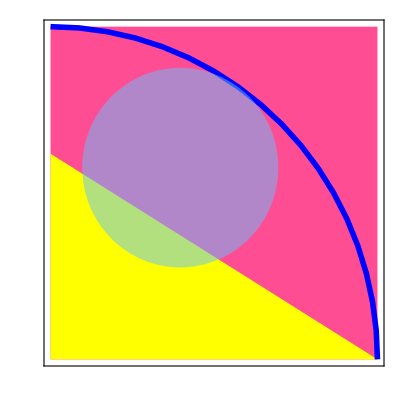

```mathematica
SETTING1by1 = { 
			AspectRatio-> 1,
			PlotRange ->  { {0,1}, {0,1} },

			FrameTicks-> None,
			Frame-> True,
			FrameStyle->Directive[Black,Thickness[0.005]]
                        };

gr = (1 + Sqrt[5])/2;
angel = Pi / 2 * (1 / gr);

myMotief = {
	{RGBColor[255/255,77/255,148/255], Polygon[{{0,0},{0,1},{1,1},{1,0}}]},
	{Yellow, Triangle[{{0,0},{0,1/gr},{1,0}}]},
	{Blue, Thickness[0.01],Circle[ {0,0}, 1, {0, Pi/2} ] },
	{RGBColor[102/255,194/255,255/255], Opacity[0.5], Disk[{0.7* Cos[angel],0.7* Sin[angel]}, 0.3]}
}

Graphics[ {myMotief},SETTING1by1 ]
```

## Rotating and Reflecting Following tiles are the rotation and reflection results of my motif.I am showing it on a grid. rot9 is rotating the motif by 90 degrees counterclockwise. rot18 is rotating the motif by 180 degrees counterclockwise. rot27 is rotating the motif by 270 degrees counterclockwise. ref1 is reflecting by y axis. ref2 is reflecting by y = x. ref3 is reflecting by x axis. ref4 is reflecting by y = -x.

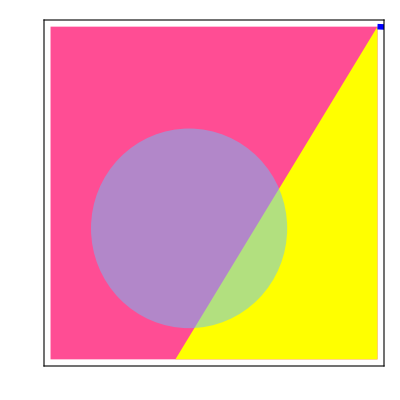
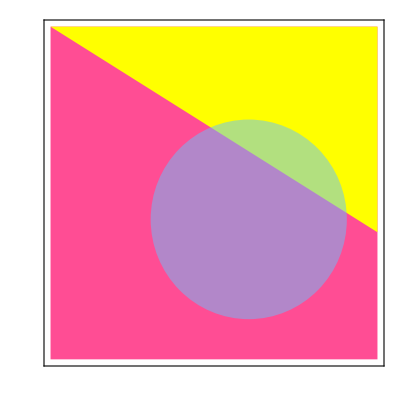
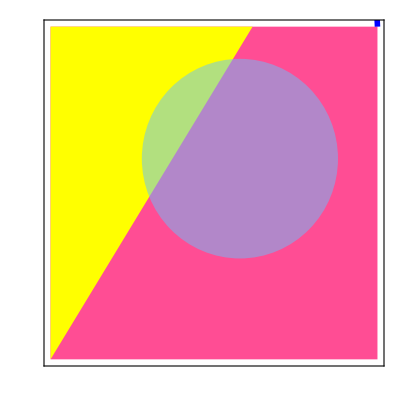
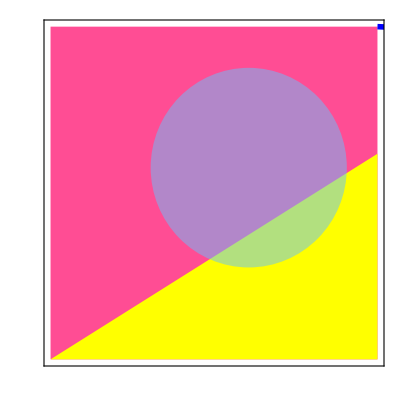
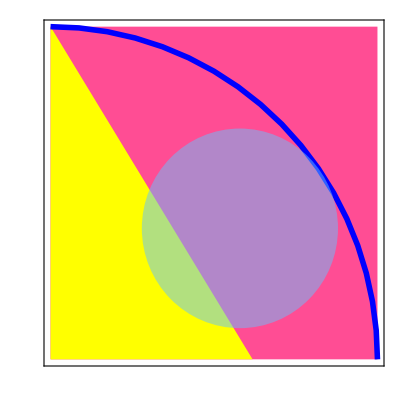
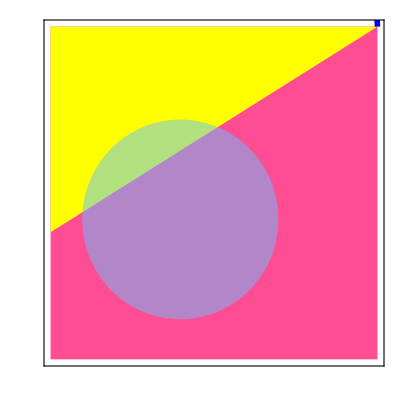
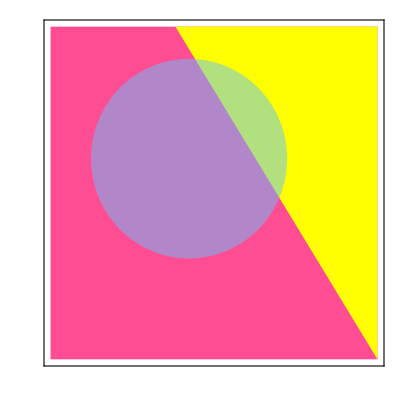
Grid[{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}]

```mathematica
ori = myMotief;

rot9 = GeometricTransformation[ ori ,  RotationTransform[ Pi/2, {1/2,1/2}]  ];
rot18 = GeometricTransformation[ ori ,  RotationTransform[ Pi, {1/2,1/2}]  ];
rot27  = GeometricTransformation[ ori ,  RotationTransform[ 3 * Pi/2, {1/2,1/2}]  ];

ref1 = GeometricTransformation[ori, ReflectionTransform[{1,0},{1/2,1/2}]];
ref2 = GeometricTransformation[ori, ReflectionTransform[{-1,1},{1/2,1/2}]];
ref3 = GeometricTransformation[ori, ReflectionTransform[{0,-1},{1/2,1/2}]];
ref4 = GeometricTransformation[ori, ReflectionTransform[{1,1},{1/2,1/2}]];

Grid[{Graphics[ori,SETTING1by1]}, 
{Graphics[rot9,SETTING1by1]},
{Graphics[rot18,SETTING1by1]},
{Graphics[rot27,SETTING1by1]},
{Graphics[ref1,SETTING1by1]},
{Graphics[ref2,SETTING1by1]},
{Graphics[ref3,SETTING1by1]},
{Graphics[ref4,SETTING1by1]}]
```

## Making Super Tiles I am building a function to make super-tiles which consists of 4 motifs from what we have constructed.

```mathematica
makeSuperTile[{x_, y_, u_, v_}] :={ 
									GeometricTransformation[x, TranslationTransform[ {0,1}]], 
									GeometricTransformation[y, TranslationTransform[ {1,1}]],
									GeometricTransformation[u, TranslationTransform[ {1,0}]], 
									GeometricTransformation[v, TranslationTransform[ {0,0}]]}
```

## Creating Scheme

### Scheme 1 This super tile seems to form a wave like pattern. There is a rotative symmetry in the super tile. Rotating 180 degree will return to the original super tile. No reflective symmetry in the super tile.

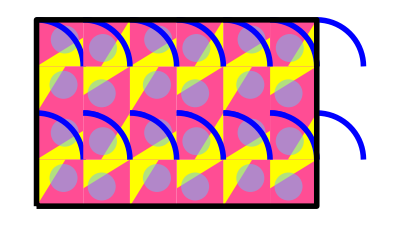

```mathematica
superTile = makeSuperTile[ { ref1, rot9, ref3, rot27} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```

### Scheme 2 This super tile forms a closed blue circle. There is a rotative symmetry in the super tile. Rotating 90 degree will return to the original super tile. No reflective symmetry in the super tile.

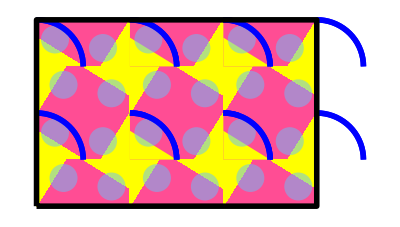

```mathematica
superTile = makeSuperTile[ { ori, rot9, rot18, rot27} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```

### Scheme 3 This super tile forms a fan like pattern. There is a rotative symmetry in the super tile. Rotating 90 degree will return to the original super tile. No reflective symmetry in the super tile.

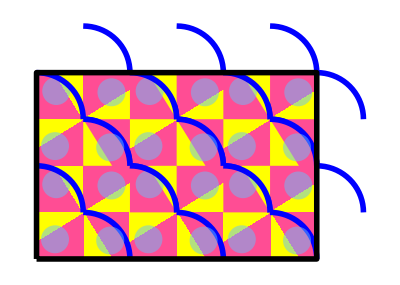

```mathematica
superTile = makeSuperTile[ { ref4, ref1, ref2, ref3} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```

### Scheme 4 This looks like a fish scale pattern. The super tile has no rotative symmetry. we can, however, find a reflective symmetry on x axis in the super tile. There is a glide reflection in the final output graph.

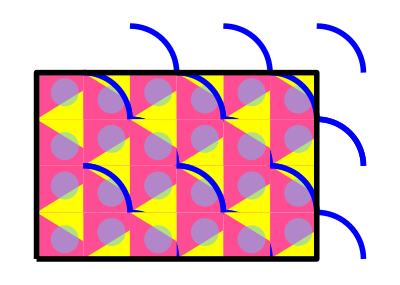

```mathematica
superTile = makeSuperTile[ { ref1, rot18, ref1, rot18} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```

### Scheme 5 This super tile also form a circle. There is no reflective rotation involved. While, we can find a reflection on y axsis on the super tile.

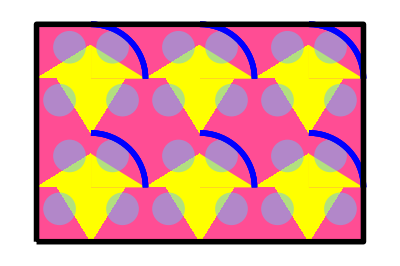

```mathematica
superTile = makeSuperTile[ { ref1, ori, rot27, ref4} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```

### Scheme 6 This scheme also has a fish scale pattern. Again, we have reflective symmetry in the super tile. While, we have no rotational symmetry. Finally, we can find a glide symmetry in the final graph.

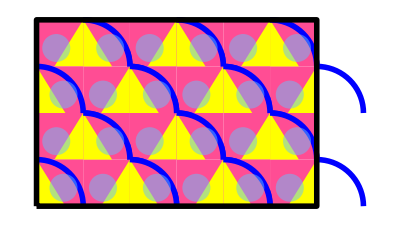

```mathematica
superTile = makeSuperTile[ { rot9, ref2, rot9, ref2} ];
Graphics[{Table[GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}],
		  Thickness[0.01], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]}]
```